# Introduction to Mathematica programming and scientific visualization

### By Renan Cabrera

-Graphics3D-

## Philosophy

## Unified Structure

Everything is an expression composed of a Head and a list of elements

```mathematica
a+b
```

a+b

```mathematica
FullForm[a+b]
```

Plus[a,b]

```mathematica
FullForm[a*b]
```

Times[a,b]

```mathematica
a+b+c//FullForm
```

Plus[a,b,c]

One of the most important expressions in Mathematica is the List

```mathematica
list={1,2,3,4};
```

```mathematica
list//FullForm
```

List[1,2,3,4]

Lists  can be nested to represent matrices

```mathematica
{list,list,list}//MatrixForm
```

(1 | 2 | 3 | 4
1 | 2 | 3 | 4
1 | 2 | 3 | 4)

Raw numbers are the exception

```mathematica
1//FullForm
```

1

Preventing from prompt echo: use semicolon

```mathematica
a+b;
```

Everything is an expression, so high degree of personalization of graphics

```mathematica
ChemicalData["Caffeine","MoleculePlot"]
```

-Graphics3D-

In similar way we can change the instrument of a midi sound file

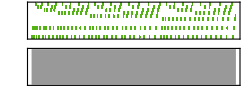

```mathematica
Interpreter["Sound"][File["ExampleData/scaleprogression.mid"]]
```

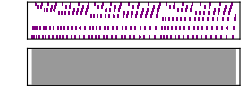

```mathematica
Interpreter["Sound"][File["ExampleData/scaleprogression.mid"]]/.{"Harp"-> "Piano"}
```

## Functions, Functional Programming, and Rules

### Assigning values. Direct method

Initial value of f

```mathematica
f=1
```

1

```mathematica
g=f
```

1

Changing the value of f

```mathematica
f= 2
```

2

The value of g is still the same

```mathematica
g
```

1

This is the usual method in numerical programs.

### Assigning values in a persistent manner

The value can be assigned persistently.

```mathematica
G:=f
```

```mathematica
G
```

2

changing the value of f

```mathematica
f=3
```

3

changes the value of G

```mathematica
G
```

3

The value of G is linked to the value of f. 

In fact, whenever we call G, Mathematica goes back to the definition of G looking for an update. In this sense, the evaluation is delayed.

### Definition of functions. Direct method

a variable must be clean to assign functions. We clean the values of a variable as follows

```mathematica
ClearAll[f,g,G]
```

```mathematica
f[x_]=Sin[x]+2
```

2+Sin[x]

NOTE:  The variable  x must be followed by _ in the definition

Evaluation leads to

```mathematica
f[π/2]
```

3

### Definition of functions. Delayed method

Sometimes we must delay the evaluation. One reason is that the function may require a numerical value

```mathematica
g[x_]:=NIntegrate[  Exp[-y^2],{y,-5,x} ]
```

```mathematica
g[0]
```

0.886227

Otherwise, the numerical integrator returns an error with a symbolic limit

```mathematica
NIntegrate[  Exp[-y^2],{y,-5,x} ]
```

NIntegrate::nlim: y = x is not a valid limit of integration.

NIntegrate[Exp[-y^2],{y,-5,x}]

This means that the function must be delayed.

Example : making the factorial function

```mathematica
factorial[0]=1;
```

```mathematica
factorial[n_]:=n factorial[n-1]
```

```mathematica
factorial[2]
```

2

```mathematica
factorial[3]
```

6

### Functional Programming

User defined functions do not distribute in data arrays by default. One must set the desired behavior or apply some functions that generate certain distributions.

```mathematica
ClearAll[f,g,G]
```

```mathematica
f[{1,2,3,4}]
```

f[{1,2,3,4}]

#### Map

Element-wise distribution on a single array

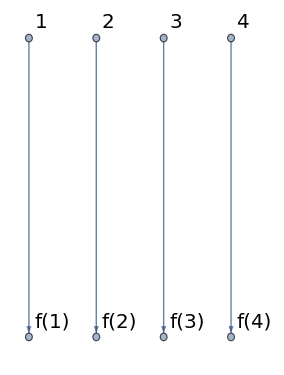

```mathematica
Graph[{1->f[1],2->f[2],3->f[3],4->f[4]},VertexLabels->"Name",VertexLabelStyle->Directive[Black,Italic,20]]
```

```mathematica
Map[ f ,{1,2,3,4} ]
```

{f[1],f[2],f[3],f[4]}

#### MapThread

Element-wise distribution on multiple arrays

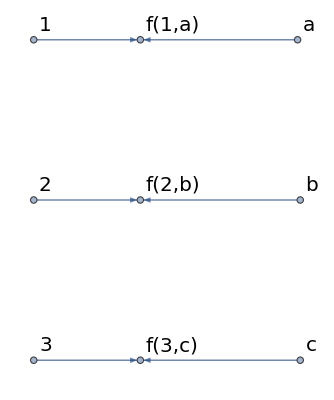

```mathematica
Graph[{1->f[1,a],a-> f[1,a],2->f[2,b],b-> f[2,b],3->f[3,c],c-> f[3,c]},VertexLabels->"Name",VertexLabelStyle->Directive[Black,Italic,20],VertexCoordinates->{
{0.25,-0.25001000000000007},{1.25,-0.25001},{2.725001,-0.25001000000000007},
{0.25,-1.7500300000000002},{1.25001,-1.75003},{2.75001,-1.7500300000000002},
{0.25,-3.2500},{1.25002,-3.25001},{2.75002,-3.25001}}]
```

```mathematica
MapThread[
f,
{{1,2,3},
{a,b,c}}]
```

{f[1,a],f[2,b],f[3,c]}

Simple application: Joining two matrices

```mathematica
MapThread[Join,{
({{a11, a12}, {a21, a22}}),({{b11, b12}, {b21, b22}})
}]//MatrixForm
```

(a11 | a12 | b11 | b12
a21 | a22 | b21 | b22)

Element-wise distribution on multiple matrices

```mathematica
MapThread[f,{
({{a11, a12}, {a21, a22}}),({{b11, b12}, {b21, b22}})
},2]//MatrixForm
```

(f[a11,b11] | f[a12,b12]
f[a21,b21] | f[a22,b22])

#### Outer

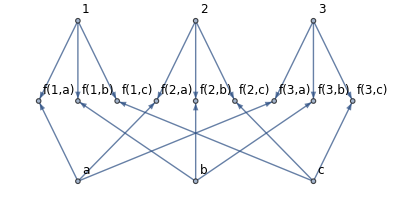

```mathematica
Graph[
{1->f[1,a],a->f[1,a],1-> f[1,b],b-> f[1,b],1-> f[1,c],c-> f[1,c],
2->f[2,a],a->f[2,a],2-> f[2,b],b-> f[2,b],2-> f[2,c],c-> f[2,c],
3->f[3,a],a->f[3,a],3-> f[3,b],b-> f[3,b],3-> f[3,c],c-> f[3,c]},
 VertexLabels->"Name",VertexLabelStyle->Directive[Black,Italic,12] ,
VertexCoordinates->{
{0.,2.},{-1.,0.},{0.,-2.},{0.,0},{3.,-2.},{1.,0.},
{6.,-2},
{3.,2},{2.,0.},{3,0},{4.,0},
{6.,2},{5.,0.},{6.,0.},{7.,0.}}]
```

```mathematica
Outer[f,{1,2,3},{a,b,c}]//MatrixForm
```

(f[1,a] | f[1,b] | f[1,c]
f[2,a] | f[2,b] | f[2,c]
f[3,a] | f[3,b] | f[3,c])

#### Inner (Reduction)

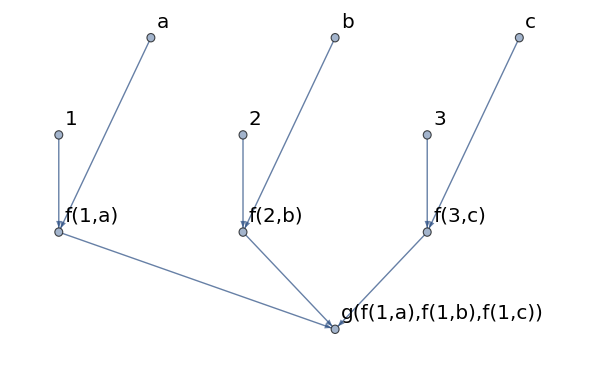

```mathematica
Graph[{1->f[1,a],a-> f[1,a],2->f[2,b],b-> f[2,b],3->f[3,c],c-> f[3,c],f[1,a]-> g[f[1,a],f[1,b],f[1,c]],
f[2,b]-> g[f[1,a],f[1,b],f[1,c]], f[3,c]-> g[f[1,a],f[1,b],f[1,c]]},
VertexLabels->"Name",VertexLabelStyle->Directive[Black,Italic,20],
VertexCoordinates->{{0,2.},{0,1.},
{1.,3.},{2,2.},{2,1.},{3.,3.},{4.,2.},{4.,1.},{5.,3.},{3.,0.}}]
```

Example

```mathematica
divergence[vec_,vars_]:=Inner[D,vec,vars,Plus]
```

```mathematica
divergence[{fx[x,y,z],fy[x,y,z],fz[x,y,z]},{x,y,z}]
```

fz^(0,0,1)[x,y,z]+fy^(0,1,0)[x,y,z]+fx^(1,0,0)[x,y,z]

#### Nest

```mathematica
Nest[f,1,5]
```

f[f[f[f[f[1]]]]]

#### Fold

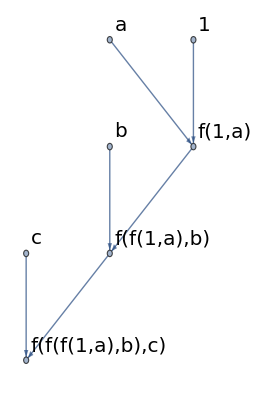

```mathematica
Graph[{  a-> f[1,a],1-> f[1,a]  , f[1,a]-> f[f[1,a],b], b-> f[f[1,a],b] , f[f[1,a],b]-> f[f[f[1,a],b],c], c-> f[f[f[1,a],b],c]},
VertexLabels->"Name",VertexLabelStyle->Directive[Black,Italic,20]]
```

```mathematica
Fold[f,1,{a,b,c,d}]
```

f[f[f[f[1,a],b],c],d]

### Definition of Functions

In the previous sections we learned how to define functions.For example

```mathematica
function1[x_]=Sin[x]+1;
```

A second method to do the same is

```mathematica
function2 = Function[{x},  Sin[x]+1];
```

```mathematica
function2[x]
```

1+Sin[x]

A third method is (lambda functions)

```mathematica
function3 = ((Sin[#]+1)&)
```

Sin[#1]+1&

We can evaluate functions in different alternative ways. For example:

Prefix form:

```mathematica
function3@y
```

1+Sin[y]

Postfix form

```mathematica
y//function3
```

1+Sin[y]

The middle form of a function is

```mathematica
{1,2,3}~Join~{4,5,6}
```

{1,2,3,4,5,6}

### Rules: Part 1

Substitution of variables is a very important operation in symbolic calculation. This is done in Mathematica with the help of rules. Let us define an arbitrary expression

```mathematica
A=a+b+c
```

a+b+c

The variable a can be replaced by a number (The arrow symbol  is obtained by typing “-“ followed by “>”)

```mathematica
A/.{a-> 2}
```

2+b+c

Let us apply the same rule many times

```mathematica
{a,a,a+1,a+2}/.{a-> RandomReal[]}
```

{0.929819,0.929819,1.92982,2.92982}

This previous example is telling us that the random number was actually evaluated only once.

An alternative substitution can be done by delaying the evaluation (The arrow symbol with dots is obtained by typing “:” followed by “>”)

```mathematica
{a,a,a+1,a+2}/.{a:>  RandomReal[]}
```

{0.69894,0.908729,1.57113,2.48478}

Be careful when dealing with complex numbers. The following substitution does not work

```mathematica
1+I/.{1-> a}
```

1+ⅈ

### Rules: Part 2

Rules can be extremely flexible. For example, we can restrict the substitutions to those that fit a pattern (expressions with underscore)

Rule applied to the Sin functions:

```mathematica
Sin[1]+ 2Sin[b]+ Sin[c] /.{Sin[x_]-> W[x]}
```

W[1]+2 W[b]+W[c]

Rule applied to the Sin functions evaluated on a numeric value:

```mathematica
Sin[1]+ 2Sin[b]+ Sin[c] /.{Sin[x_?NumericQ]->   W[x]}
```

2 Sin[b]+Sin[c]+W[1]

Rule applied to the terms multiplied by 2:

```mathematica
Sin[1]+ 2Sin[b]+ Sin[c] /.{2f_[x_]->   2W[x]}
```

Sin[1]+Sin[c]+2 W[b]

Rules can be applied to every level of the Mathematica expression:

```mathematica
Sin[1]+ 2 Sin[b]+ Tan[c] /.{x_?AtomQ-> q}
```

q[q[q],q[q,q[q]],q[q]]

Rules can be applied to functions. For example

```mathematica
f[x]+ f''[x]/.{  f-> (Exp[g[#]]&) }
%//Simplify
```

ⅇ^g[x]+ⅇ^g[x] g'[x]^2+ⅇ^g[x] g''[x]

ⅇ^g[x] (1+g'[x]^2+g''[x])

## Symbolic Computation

### Calculus

Derivatives

```mathematica
D[Sin[x],x]
```

Cos[x]

Integrals

```mathematica
Integrate[Sin[x],x]
```

-Cos[x]

```mathematica
Integrate[ Exp[-a x^2],{x,-∞,∞},Assumptions->{a>0}]
```

(√π)/(√a)

```mathematica
Integrate[BesselJ[2,x],x]
```

1/24 x^3 HypergeometricPFQ[{3/2},{5/2,3},-x^2/4]

### Differential equations and differential operators

#### Differential equations. Method 1

```mathematica
sol1=DSolve[  f''[x]+ x^2 f[x]==0 ,f[x],x]
```

{{f[x]→C[2] ParabolicCylinderD[-1/2,(-1+ⅈ) x]+C[1] ParabolicCylinderD[-1/2,(1+ⅈ) x]}}

Advantage: Direct manipulation

```mathematica
sol1//FunctionExpand
```

{{f[x]→2^(1/4) ⅇ^((ⅈ x^2)/2) C[2] HermiteH[-1/2,-((1-ⅈ) x)/(√2)]+2^(1/4) ⅇ^(-(ⅈ x^2)/2) C[1] HermiteH[-1/2,((1+ⅈ) x)/(√2)]}}

```mathematica
f[x]/.sol1
```

{C[2] ParabolicCylinderD[-1/2,(-1+ⅈ) x]+C[1] ParabolicCylinderD[-1/2,(1+ⅈ) x]}

Disadvantage: Substitution in differential equations

```mathematica
f'[x]/.sol1
```

{f'[x]}

#### Differential equations. Method 2

```mathematica
sol2=DSolve[  f''[x]+ x^2 f[x]==0 ,f,x]
```

{{f→Function[{x},C[2] ParabolicCylinderD[-1/2,(-1+ⅈ) x]+C[1] ParabolicCylinderD[-1/2,(1+ⅈ) x]]}}

Disadvantage: Not directly manipulable

```mathematica
sol2//FunctionExpand
```

{{f→Function[{x},C[2] ParabolicCylinderD[-1/2,(-1+ⅈ) x]+C[1] ParabolicCylinderD[-1/2,(1+ⅈ) x]]}}

Advantage: Substitution in differential equations

```mathematica
f[x]+a f'[x]/.sol2
```

{C[2] ParabolicCylinderD[-1/2,(-1+ⅈ) x]+C[1] ParabolicCylinderD[-1/2,(1+ⅈ) x]+a ((-1+ⅈ) C[2] ((-1/2+ⅈ/2) x ParabolicCylinderD[-1/2,(-1+ⅈ) x]-ParabolicCylinderD[1/2,(-1+ⅈ) x])+(1+ⅈ) C[1] ((1/2+ⅈ/2) x ParabolicCylinderD[-1/2,(1+ⅈ) x]-ParabolicCylinderD[1/2,(1+ⅈ) x]))}

### Differential Operators 1

```mathematica
ExtractOperator[ψ_][w_]:= Module[{k,pre,DD},
pre=Evaluate[w/.{ψ[x]-> #,ψ'[x]-> DD[#,x], Derivative[k_][ψ][x]:> DD[#,{x,k}] }]&;
pre/.{DD-> D}
]
```

```mathematica
Commutator[F_,G_]:= Module[{ψ,pre},
pre=F[G[ψ[x]]]- G[F[ψ[x]]];
ExtractOperator[ψ]@Simplify[pre]
];
```

Defining the position and momentum operator

```mathematica
xOperator = (x#&)
```

x #1&

```mathematica
pOperator = ((-I ℏ D[#,x])&)
```

-ⅈ ℏ ∂_x #1&

```mathematica
Commutator[xOperator,pOperator[pOperator[#]]& ]
```

2 ℏ^2 ∂_x #1&

```mathematica
Commutator[pOperator,F[x]#&  ]
```

-ⅈ ℏ #1 F'[x]&

```mathematica
Commutator[ pOperator@pOperator[#]&,F[x]#&  ]
```

-ℏ^2 (2 ∂_x #1 F'[x]+#1 F''[x])&

### Differential Operators 2: Landau Levels

```mathematica
Clear@ExtractOperator
```

```mathematica
Clear@Commutator
```

```mathematica
Clear@A
```

```mathematica
ExtractOperator[ψ_][w_]:= Module[{k,pre,DD},
pre=Evaluate[w/.{
ψ[x,y,z]-> #,
 Derivative[kx_,ky_,kz_][ψ][x,y,z]:> DD[#,{x,kx},{y,ky},{z,kz}] }]&;
pre/.{DD-> D}
]
```

```mathematica
Commutator[F_,G_]:= Module[{ψ,pre},
pre=F[G[ψ[x,y,z]]]- G[F[ψ[x,y,z]]];
ExtractOperator[ψ]@Simplify[pre]
];
```

```mathematica
xOperator = (x#&);
yOperator = (y#&);
zOperator = (z#&);
```

```mathematica
pxOperator = ((-I ℏ D[#,x])&);
pyOperator = ((-I ℏ D[#,y])&);
pzOperator = ((-I ℏ D[#,z])&);
```

```mathematica
Commutator[xOperator,pxOperator]
```

ⅈ ℏ #1&

```mathematica
Commutator[xOperator,pOperator[pOperator[#]]& ]
```

2 ℏ^2 ∂_({x,1},{y,0},{z,0}) #1&

```mathematica
uxOperator = ( 1/m( pxOperator[#]- 1/c A1[x,y,z]#)&);
uyOperator = ( 1/m( pyOperator[#]- 1/c A2[x,y,z]#)&);
uzOperator = ( 1/m( pzOperator[#]- 1/c A3[x,y,z]#)&);
```

```mathematica
hamiltonianOperator=(m/2 uxOperator@uxOperator[#]+m/2 uyOperator@uyOperator[#]+m/2 uzOperator@uzOperator[#] + V[x,y,z]# &)
```

1/2 m uxOperator[uxOperator[#1]]+1/2 m uyOperator[uyOperator[#1]]+1/2 m uzOperator[uzOperator[#1]]+V[x,y,z] #1&

```mathematica
hamiltonianOperator[ψ[x,y,z]]//Simplify
```

1/(2 c^2 m)(A1[x,y,z]^2 ψ[x,y,z]+A2[x,y,z]^2 ψ[x,y,z]+A3[x,y,z]^2 ψ[x,y,z]+2 c^2 m V[x,y,z] ψ[x,y,z]+ⅈ c ℏ ψ[x,y,z] A3^(0,0,1)[x,y,z]+2 ⅈ c ℏ A3[x,y,z] ψ^(0,0,1)[x,y,z]-c^2 ℏ^2 ψ^(0,0,2)[x,y,z]+ⅈ c ℏ ψ[x,y,z] A2^(0,1,0)[x,y,z]+2 ⅈ c ℏ A2[x,y,z] ψ^(0,1,0)[x,y,z]-c^2 ℏ^2 ψ^(0,2,0)[x,y,z]+ⅈ c ℏ ψ[x,y,z] A1^(1,0,0)[x,y,z]+2 ⅈ c ℏ A1[x,y,z] ψ^(1,0,0)[x,y,z]-c^2 ℏ^2 ψ^(2,0,0)[x,y,z])

The vector potential of a homogeneous magnetic field

```mathematica
AHomogeneous=Cross[{0,0,B3},{x,y,z}]/2
```

{-(B3 y)/2,(B3 x)/2,0}

```mathematica
Curl[AHomogeneous,{x,y,z}]
```

{0,0,B3}

Applying this vector potential to the Hamiltonian

```mathematica
hamiltonianOperator[ψ[x,y]]/.{
V[x,y,z]-> 0,
 A1->  Function[{x,y,z},  -B*y ],
A2-> Function[{x,y,z},0],
A3-> Function[{x,y,z},0] }//Simplify

hamiltonianY= Exp[-I k x](%/.{ψ-> Function[{x,y},  Exp[I k x]   ϕ[y]] })//Simplify
```

(B^2 y^2 ψ[x,y]-c ℏ (c ℏ ψ^(0,2)[x,y]+2 ⅈ B y ψ^(1,0)[x,y]+c ℏ ψ^(2,0)[x,y]))/(2 c^2 m)

((B y+c k ℏ)^2 ϕ[y]-c^2 ℏ^2 ϕ''[y])/(2 c^2 m)

we obtain the Landau levels

```mathematica
DSolve[hamiltonianY==ϵ ϕ[y],ϕ[y],y]//FunctionExpand//Simplify
```

{{ϕ[y]→2^(1/4-(c m ϵ)/(2 B ℏ)) ⅇ^(-(B y+c k ℏ)^2/(2 B c ℏ)) (2^((c m ϵ)/(B ℏ)) ⅇ^((B y+c k ℏ)^2/(B c ℏ)) C[2] HermiteH[-1/2-(c m ϵ)/(B ℏ),(ⅈ (B y+c k ℏ))/(√B √c √ℏ)]+C[1] HermiteH[-1/2+(c m ϵ)/(B ℏ),(B y+c k ℏ)/(√B √c √ℏ)])}}

with the proper energy quantization

```mathematica
Last@Solve[-1/2+(c m ϵ)/(B ℏ)==n,ϵ]/.{B-> m c Subscript[ω, c] }
```

{ϵ→1/2 (1+2 n) ℏ ω_c}

### Differential Operators 3: Curvilinear coordinates

```mathematica
xyTorθRule={x-> r Cos[θ], y-> r Sin[θ]}
```

{x→r Cos[θ],y→r Sin[θ]}

```mathematica
Map[Equal@@#&,xyTorθRule];
rθToxyRule= Simplify[Last@Solve[%,{r,θ}]/.{C[1]->0}]
```

{r→√(x^2+y^2),θ→ArcTan[x/(√(x^2+y^2)),y/(√(x^2+y^2))]}

```mathematica
ChainRuleOperator[ψ_][W_]:=Module[{rule,pre,DD},
rule={
Derivative[1,0][ψ][x,y]:>   ( D[r/.rθToxyRule,x]DD[#, r]  + D[θ/.rθToxyRule,x]DD[#, θ]  ),
Derivative[0,1][ψ][x,y]:>   ( D[r/.rθToxyRule,y]DD[#, r]  + D[θ/.rθToxyRule,y]DD[#, θ]  )};

pre=Simplify[(W/.rule)/.xyTorθRule,Assumptions->{r>0}];
(Evaluate[pre]&)/.{DD->D}
]
```

```mathematica
D[ψ[x,y],x]
gradxOp=ChainRuleOperator[ψ][%]
```

ψ^(1,0)[x,y]

Cos[θ] ∂_r #1-(∂_θ #1 Sin[θ])/r&

```mathematica
D[ψ[x,y],y]
gradyOp=ChainRuleOperator[ψ][%]
```

ψ^(0,1)[x,y]

(Cos[θ] ∂_θ #1)/r+∂_r #1 Sin[θ]&

Gradient

```mathematica
{D[ψ[x,y],x],D[ψ[x,y],y]}
grad=ChainRuleOperator[ψ][%]
```

{ψ^(1,0)[x,y],ψ^(0,1)[x,y]}

{Cos[θ] ∂_r #1-(∂_θ #1 Sin[θ])/r,(Cos[θ] ∂_θ #1)/r+∂_r #1 Sin[θ]}&

Laplacian

```mathematica
gradxOp@gradxOp[ψ[r,θ]]+gradyOp@gradyOp[ψ[r,θ]]//Simplify//Expand
```

(ψ^(0,2)[r,θ])/r^2+(ψ^(1,0)[r,θ])/r+ψ^(2,0)[r,θ]

## Numerics

### Arbitrary precision

The numerical evaluation is achieved by the function N with the option of arbitrary numerical precision

```mathematica
Sin[π/8]
N[%,24]
```

Sin[π/8]

0.38268343236508977172846

It is possible to specify the precision using the ` symbol

```mathematica
1.`32/3.`32
```

0.3333333333333333333333333333333

### Complex numbers basics

```mathematica
Conjugate[1+I]
```

1-ⅈ

```mathematica
Conjugate[a]
```

Conjugate[a]

```mathematica
Simplify[
Conjugate[a]
,Assumptions->{Element[a,Reals]}]
```

a

Numerical Optimization

Random matrices

## Scientific Visualization

### Basics

Before everything, let us only maintain only one step behind in the history of evaluation in order to improve performance

```mathematica
$HistoryLength=1
```

1

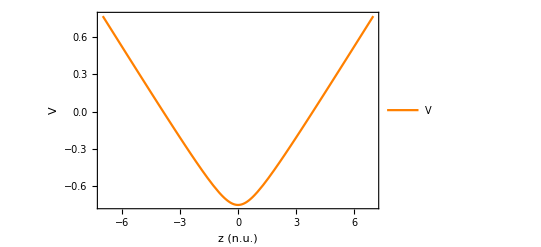

```mathematica
potentialPlot=Plot[
 Sqrt[z^2+1]/4-1  ,{z,-7,7},
BaseStyle->{FontSize->12,FontSlant->Italic},
PlotRange->All,FrameLabel->{"z (n.u.)","V"},
PlotLegends->Placed[{Style["V",Italic]},Top],
Frame->True,PlotStyle->{Orange}]
```

The set of options that characterize this figure is found with AbsoluteOptions

```mathematica
AbsoluteOptions[potentialPlot];
```

Ticks::ticks: {Automatic,Automatic} is not a valid tick specification.

General::stop: Further output of Ticks::ticks will be suppressed during this calculation.

The internal Mathematica representation of the plot is found as

```mathematica
InputForm[potentialPlot];
```

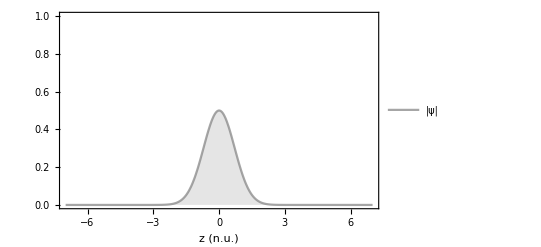

```mathematica
statePlot=Plot[ Exp[-z^2]/2,{z,-7,7},
PlotRange->{0,1},
FrameLabel->{"z (n.u.)",""},
Filling->Bottom,Frame->True,
PlotLegends->Placed[{"|ψ|"},Top],
PlotStyle->{Gray,Opacity[0.7]}]
```

Two plots can be superimposed with Show

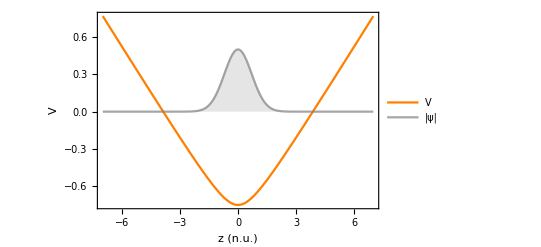

```mathematica
Show[  potentialPlot , statePlot]
```

This way to superimpose plots is intelligent in the sense that the validity of each plot is respected. 
The options are merged with the options of the first plot ruling out over the second one.

Multiple curves can be plotted

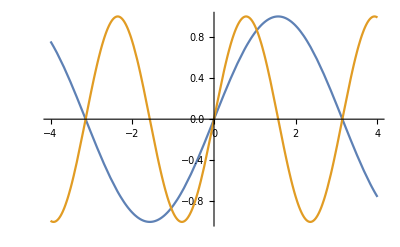

```mathematica
Plot[{Sin[x],Sin[2x]},{x,-4,4}]
```

The following plot should be the same, but it is not

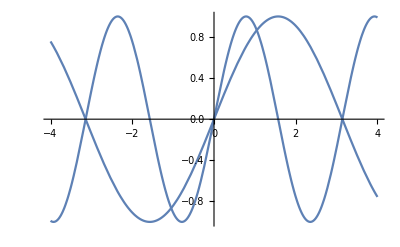

```mathematica
Plot[
Table[Sin[n x],{n,1,2}],
{x,-4,4},PlotLegends->"Expressions"]
```

The correct behavior is obtained by applying an extra Evaluate function that forces the evaluation before executing the plotting. 
This is an important key point to remember specially for demanding plots that otherwise would demand too much evaluation time.

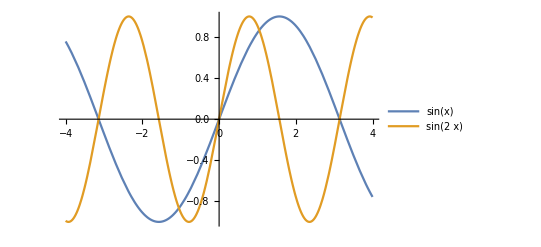

```mathematica
Plot[
Evaluate[
Table[Sin[n x],{n,1,2}]
],
{x,-4,4},PlotLegends->"Expressions"]
```

### Objects

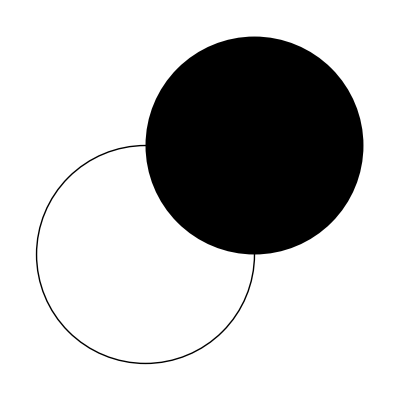

```mathematica
Graphics[
{Circle[{0,0},1], Disk[{1,1},1]}
]
```

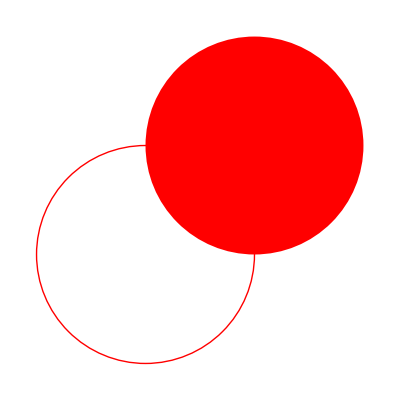

```mathematica
Graphics[
{
Red,
Circle[{0,0},1], Disk[{1,1},1]
}
]
```

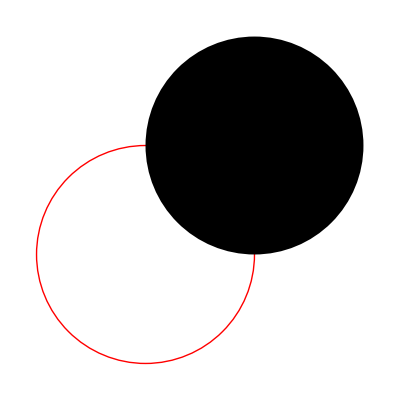

```mathematica
Graphics[
{
{Red,Circle[{0,0},1]},
 Disk[{1,1},1]
}
]
```

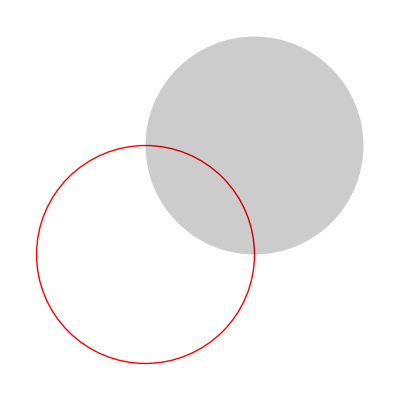

```mathematica
Graphics[
{
{Red,Circle[{0,0},1]},
{ Opacity[0.2],Disk[{1,1},1]}
}
]
```

### Stream plots

```mathematica
currentJ[{r_,B_,c_,m_,ℏ_},{t_,x_,y_}]={-(r ω^2 (-c (-2 c (B+c m ω)+ω^2 ℏ) Sin[t ω]+2 B r ω^2 (y Cos[2 t ω]-x Sin[2 t ω])))/(8 c^2 π √((c-r ω) (c+r ω))),(r ω^2 (c (2 c (B+c m ω)-ω^2 ℏ) Cos[t ω]-2 B r ω^2 (x Cos[2 t ω]+y Sin[2 t ω])))/(8 c^2 π √((c-r ω) (c+r ω)))}/.{ω->(c^2 m-√(c^4 m^2+2 B c ℏ))/ℏ}//Simplify;
```

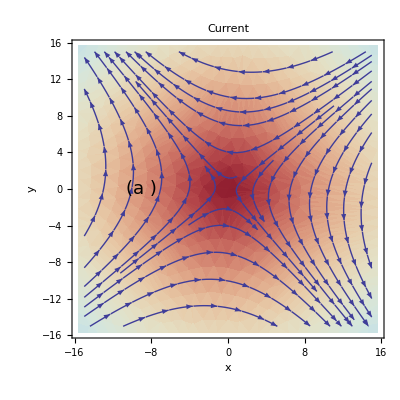

```mathematica
StreamDensityPlot[
currentJ[{2,0.1,1,1,1},{1,x,y}]
,{x,-15.,15.},{y,-15,15},
StreamStyle->{Orange},BaseStyle->{FontSize->14},PlotLegends->Automatic,
StreamPoints->24,
PlotLabel->"Current",
FrameLabel->{"x","y"},
Epilog->{ Inset[ Style["(a )",FontSize->18],{-9,0}] },
ColorFunctionScaling->False,
ColorFunction->(ColorData["ThermometerColors"][1-10000#5]&)]
```

```mathematica
im=Image[Graphics[
{Opacity[0.5],PointSize[0.1],Table[{Hue[RandomReal[]], Disk[{RandomReal[],RandomReal[]},0.1]},{20} ]}
],ImageSize->300];

LineIntegralConvolutionPlot[
{currentJ[{2,0.1,1,1,1},{1,x,y}],im}
,{x,-15.,15.},{y,-15,15},RasterSize->120,
LineIntegralConvolutionScale->8,
ImageSize->300]
```

-Graphics-

### 3D

#### Drawing a 3 D surface as a revolution in the z axis

```mathematica
potential[z_]=(-2+(3 z^6)/((1+z^4)^(7/4))+(2 z^6)/((1+z^4)^(3/2))-(3 z^2)/((1+z^4)^(3/4)))/(2 √(1-z^6/((1+z^4)^(3/2))));
```

```mathematica
potentialPlot=RevolutionPlot3D[
{3.3potential[z],z},{z,-5,5},
PlotRange->{{-5,5},{-5,5},{-5,5}},
MeshStyle->{ Gray},PlotPoints->{60,60},
ColorFunction->(RGBColor[1-#6/2,1-#6/2,1-#6/2]&),BoxRatios->{5,5,7},
BaseStyle->{FontSize->12,FontSlant-> Italic},
RegionFunction->Function[{x,y,z,t,θ,r},Evaluate[2.5<θ<2Pi]],
AxesLabel->{"x (n.u.)","y (n.u.)","z (n.u.)"}]
```

-Graphics3D-

Superimposing on a volume rendering of a Gaussian

```mathematica
statePlot=DensityPlot3D[
Evaluate[(Exp[-(  (x)^2 + (y)^2 + 2z^2)/4])]
,{x,-5,5},{y,-5,5},{z,-5,5},OpacityFunction->(#^(1.7)&)];
```

```mathematica
Show[potentialPlot,statePlot]
```

-Graphics3D-

Another example, superimposing a vector field with the volume rendering of a Gaussian

```mathematica
Show[
DensityPlot3D[
Evaluate[(Exp[-(  (x-2)^2 + (y)^2 + 2z^2)/4])]
,{x,-5,5},{y,-5,5},{z,-2,2},
BoxRatios->{5,5,2},
OpacityFunction->(#^(1.7)&)]
,
SliceVectorPlot3D[
{x,-y,z}, {z==0},{x,-5,5},{y,-5,5},{z,-2,2},Lighting->"Neutral"]
];
```

#### Drawing two planes : (a) Top plane with a density plot (b) Bottom plane with a vector field

```mathematica
state=Rasterize[DensityPlot[  Exp[-(x-2)^2-y^2],{x,-5,5},{y,-5,5} ,
PlotRange->{0,1},PlotPoints->30,
FrameTicks->{None,None},
 ColorFunction->(GrayLevel[1-#]&)]];
```

```mathematica
stateAlpha=SetAlphaChannel[state,0.6];
```

```mathematica
Show[
Graphics3D[ 
{Texture[ stateAlpha ],Polygon[{{-5,-5,5},{5,-5,5},{5,5,5},{-5,5,5}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}] }
,Lighting->"Neutral"]
,
SliceVectorPlot3D[
{x,-y,z}, {z==0},{x,-5,5},{y,-5,5},{z,-2,2},Lighting->"Neutral"]
]
```

-Graphics3D-